```mathematica
findSum[f_,stepsize_,d_]:=If[d==1,Sum[f[i],{i,0,1,stepsize}],Sum[findSum[proj[f,i],stepsize,d-1],{i,0,1,stepsize}]]

totalSum[f_,stepsize_,d_]:=stepsize^d findSum[f,stepsize,d]
```

```mathematica
explicitSum[f_,stepsize_,d_]:=stepsize^d Sum[f@@(x/@Range[d]),##]&@@Sequence[Table[{x[i],0,1,stepsize},{i,1,d}]]
(*Don't use this one*)
```

```mathematica
explicitSum[#1+#2^2 &,.005,2]
```

0.842529

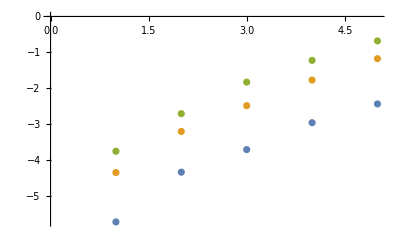

```mathematica
ListPlot[{Table[(1/n^2 Sum[i+j^2,{i,0,1,1/n},{j,0,1,1/n}]//Timing)[[1]],{n,100,300,50}],Table[(totalSum[#[[1]]+#[[2]]^2&,1/n,2]//Timing)[[1]],{n,100,300,50}],Table[(explicitSum[#[[1]]+#[[2]]^2&,1/n,2]//Timing)[[1]],{n,100,300,50}]}//Log2]
```

```mathematica
explicitSum[#1+#2^2&,1/300,2]
```

(90601 x)/90000

```mathematica
(*Conclusion: 
	It's too much effort to make a general n-D sum function be as efficient as doing it directly. The closest you can come is the total-sum one. If we're interested in 3 or 4 D, then let's just make it explicit.*)
```